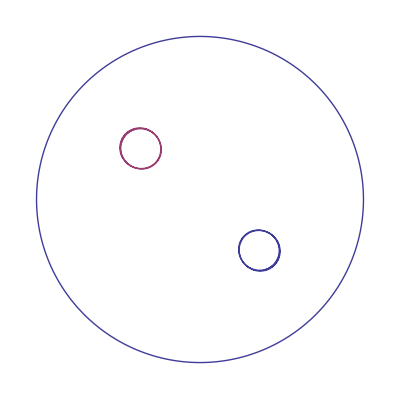

```mathematica
c=.3-2*I;
Show[Graphics[{},Method->{"TransparentPolygonMesh"->True}],
ParametricPlot[{Abs[c]*Cos[x],Abs[c]*Sin[x]},{x,0,2Pi}],
ParametricPlot[
{
{(r Re[ Sqrt[E^(I*theta)+c]])/Sqrt[2],(r Im[ Sqrt[E^(I*theta)+c]])/Sqrt[2]},{(-r Re[Sqrt[E^(I*theta)+c]])/Sqrt[2],(-r Im[Sqrt[E^(I*theta)+c]])/Sqrt[2]}
},{theta,0,2 Pi},{r,.99,1},Mesh->None,PlotLegends->Automatic,PlotStyle->Opacity[0.2],MaxRecursion->2]
]
```

```mathematica
Solve[x==y^2+c,y]
```

{{y→-√(-c+x)},{y→√(-c+x)}}